```mathematica
fA2[θ_,N_]:=Sum[Binomial[N,k] √(N-k)(Sin[θ/2])^(2k+1)(Cos[θ/2])^(2(N-k)-1),{k,0,N-1}]
```

```mathematica
fA20[θ_,N_]:=fA2[θ,N]/(√N);
fA21[θ_,N_]:=θ/2;
fA22[θ_,N_]:=√N(-θ/2+π/2);
```

General::munfl: 0.0000320891^69 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000320891^71 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000320891^73 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

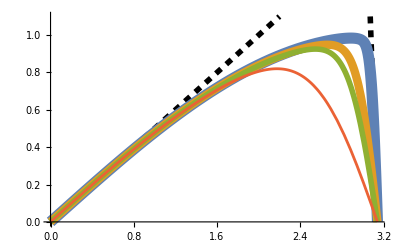

```mathematica
Plot[{fA21[θ,1000],fA22[θ,1000],fA20[θ,1000],fA20[θ,100],fA20[θ,50],fA20[θ,10]},{θ,0,π},TicksStyle->Directive[FontSize->24],PlotStyle->{{Thickness[0.01],Dashed,Black},{Thickness[0.01],Dashed,Black},{Thickness[0.02],RGBColor[0.368417,0.506779,0.709798]},{Thickness[0.015],RGBColor[0.880722,0.611041,0.142051]},{Thickness[0.01],RGBColor[0.560181,0.691569,0.194885]},{Thickness[0.005],RGBColor[0.922526,0.385626,0.209179]}},PlotRange->{0,1.1}]
```

```mathematica
Quit[]
```